# plot the k integrand & constituents

## estimate contributions from cutoff, fourier transform of smearing function, and field in k integrand for two regimes of σ

## smearing functions

```mathematica
fG[x_,σ_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftilG[k_,σ_]:=FourierTransform[fG[x,σ],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

```mathematica
fL[x_,σ_]:=σ/π 1/(x^2+σ^2)
ftilL[k_,σ_]:=FourierTransform[fL[x,σ],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

```mathematica
fx4[x_,σ_]:=(σ^3 √2)/π 1/(x^4+σ^4)
ftilx4[k_,σ_]:=FourierTransform[fx4[x,σ],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

## cutoff functions

```mathematica
cExp[k_,ε_]:=ⅇ^(-ε Abs[k]);
cSharp[k_,ε_]:=HeavisideTheta[k+ε,-k+ε];
```

## the k integrand

```mathematica
chiT1[t_]:=1/(r+T)1/2*(1+Cos[π/r(t+T/2)])
chiT2[t_]:=1/(r+T)
chiT3[t_]:=1/(r+T)1/2*(1+Cos[π/r(t-T/2)])
```

### the first interval

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ]:=tpInt1[t,k]=NIntegrate[chiT1[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T-r,t}]
```

```mathematica
tInt1[k_?NumericQ]:=tInt1[k]=α*NIntegrate[chiT1[t] tpInt1[t,k],
{t,-T-r,-T}]
```

### the second interval

```mathematica
tpInt2[t_,k_]:=Integrate[chiT2[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T,t}]
```

```mathematica
tInt2[k_]:=α*Integrate[chiT2[t] tpInt2[t,k],
{t,-T,T}]
```

### the third interval

```mathematica
tpInt3[t_?NumericQ,k_?NumericQ]:=tpInt3[t,k]=NIntegrate[chiT3[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,T,t}]
```

```mathematica
tInt3[k_?NumericQ]:=tInt3[k]=α*NIntegrate[chiT3[t] tpInt3[t,k],
{t,T,T+r}]
```

### the integrand

```mathematica
kIntegrand[k_,σ_]:=-1/π*k*(tInt1[k]+tInt2[k]+tInt3[k])
```

## plot all these ones

```mathematica
σ0=10^-4/Ω;
T=2;r=0.2;Ω=1;α=1;
```

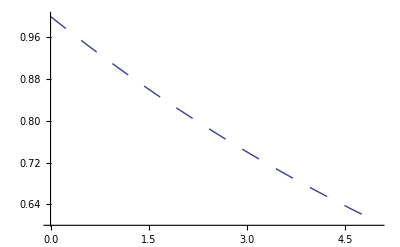

```mathematica
Plot[cExp[k,1/(10Ω)],{k,0,5},PlotStyle->{Dashing[Large],Black}]
```

### σ~σ_0

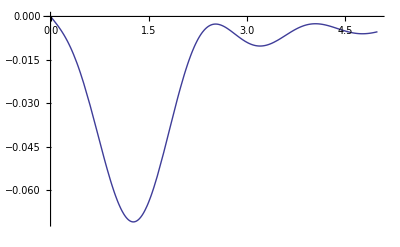

```mathematica
Plot[cExp[k,1/(10 Ω)]*ftilG[k,σ0]^2*kIntegrand[k,σ0],{k,0,5}]
```

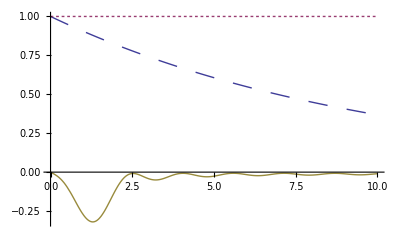

```mathematica
Plot[{cExp[k,1/(10 Ω)],ftilG[k,σ0]^2,kIntegrand[k,σ0]},{k,0,10},PlotStyle->{Dashing[Large],Dashing[Tiny],Thickness[Medium]}]
```

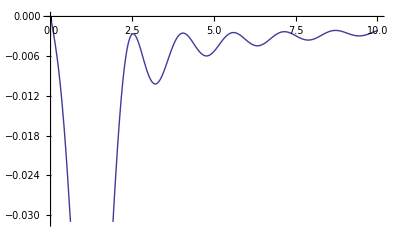

```mathematica
Plot[cExp[k,1/(10 Ω)]*ftilG[k,σ0]^2*kIntegrand[k,σ0],{k,0,10}]
```

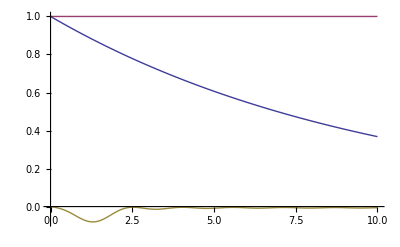

```mathematica
Plot[{cExp[k,1/(10 Ω)],ftilG[k,σ0]^2,kIntegrand[k,σ0]},{k,0,10}]
```

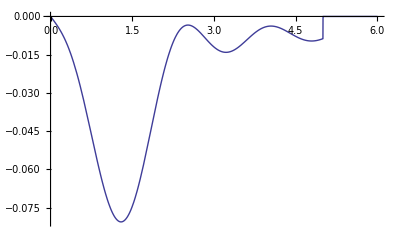

```mathematica
Plot[cSharp[k,5 Ω]*ftilG[k,σ0]^2*kIntegrand[k,σ0],{k,0,6},PlotRange->Full]
```

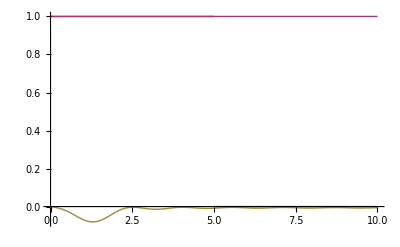

```mathematica
Plot[{cSharp[k,5 Ω],ftilG[k,σ0]^2,kIntegrand[k,σ0]},{k,0,10}]
```

### σ~10^4 σ_0

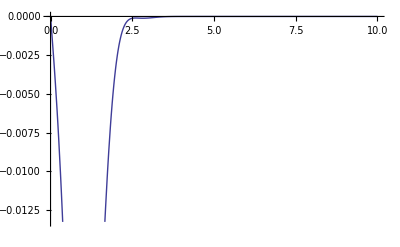

```mathematica
Plot[cExp[k,1/(10 Ω)]*ftilG[k,10^4 σ0]^2*kIntegrand[k,10^4 σ0],{k,0,10}]
```

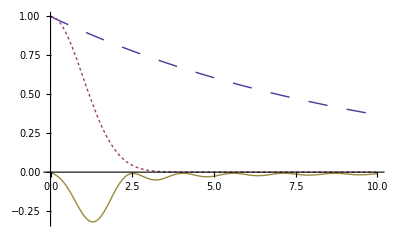

```mathematica
Plot[{cExp[k,1/(10 Ω)],ftilG[k,10^4 σ0]^2,kIntegrand[k,10^4 σ0]},{k,0,10},PlotStyle->{Dashing[Large],Dashing[Tiny],Thickness[Medium]}]
```

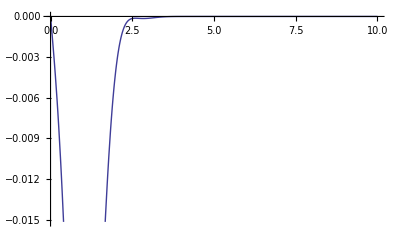

```mathematica
Plot[cSharp[k,5 Ω]*ftilG[k,10^4 σ0]^2*kIntegrand[k,10^4 σ0],{k,0,10}]
```

## lorentzian business

```mathematica
σ0=10^-4/Ω;
c=2;r=0.2;Ω=1;α=1;
A=(2*c+r+(4π)/r*Sin[r^2/(4π)])^-1;
```

### σ~σ_0

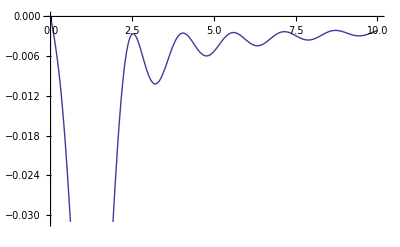

```mathematica
Plot[cExp[k,1/(10 Ω)]*ftilL[k,σ0]^2*kIntegrand[k,σ0],{k,0,10}]
```

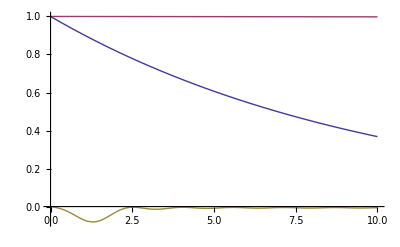

```mathematica
Plot[{cExp[k,1/(10 Ω)],ftilL[k,σ0]^2,kIntegrand[k,σ0]},{k,0,10}]
```

### σ~ σ_0

```mathematica
Plot[cExp[k,1/(10 Ω)]*ftilL[k,σ0]^2*kIntegrand[k,σ0],{k,0,10}]
```

-Graphics-

```mathematica
Plot[{cExp[k,1/(10 Ω)],ftilL[k,σ0]^2,kIntegrand[k,σ0]},{k,0,10}]
```

-Graphics-

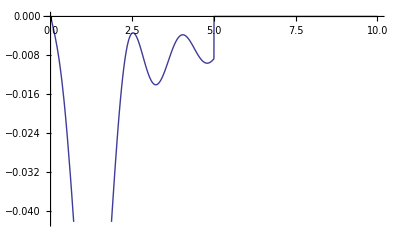

```mathematica
Plot[cSharp[k,5 Ω]*ftilL[k,σ0]^2*kIntegrand[k,σ0],{k,0,10}]
```

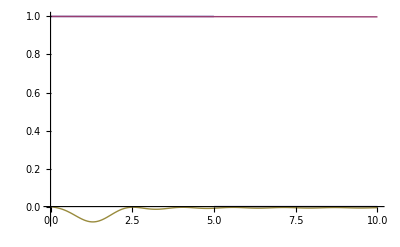

```mathematica
Plot[{cSharp[k,5 Ω],ftilL[k,σ0]^2,kIntegrand[k,σ0]},{k,0,10}]
```

### σ~10^4 σ_0

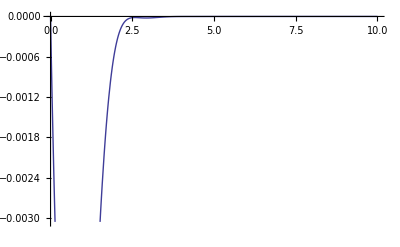

```mathematica
Plot[cExp[k,1/(10 Ω)]*ftilL[k,10^4 σ0]^2*kIntegrand[k,10^4 σ0],{k,0,10}]
```

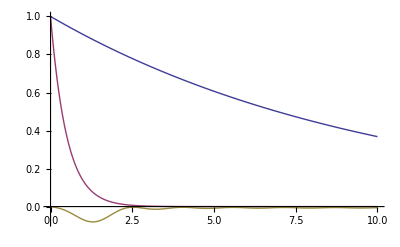

```mathematica
Plot[{cExp[k,1/(10 Ω)],ftilL[k,10^4 σ0]^2,kIntegrand[k,10^4 σ0]},{k,0,10}]
```

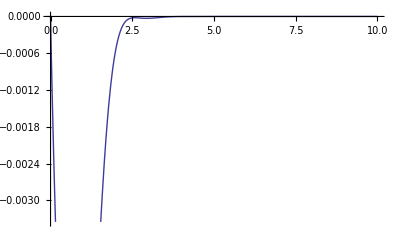

```mathematica
Plot[cSharp[k,5 Ω]*ftilL[k,10^4 σ0]^2*kIntegrand[k,10^4 σ0],{k,0,10}]
```